# Computing stabiliser channel extent for single-qubit Pauli rotations with dephasing (Figures 6.6 and 6.7 in “Advancing classical simulators by measuring the magic of quantum computation”, James R. Seddon (2021).

Eq. (6.20) and Eq. (6.19)

```mathematica
PureExtent[alpha_]:=(Cos[Pi/4-alpha]+(Sqrt[2]-1)Sin[Pi/4-alpha])^2
PureExtentGeneral[alpha_] := (Abs[Cos[Pi/4-alpha]-Sin[Pi/4-alpha]]+Sqrt[2]Abs[Sin[Pi/4-alpha]])^2

N[PureExtent[Pi/8]]
```

1.17157

Eq. (6.24)

```mathematica
Theta[phi_,p_]:= Max[(1/2) ArcSin[(1-2p)Sin[2phi+Pi/4]]-Pi/8,0]
```

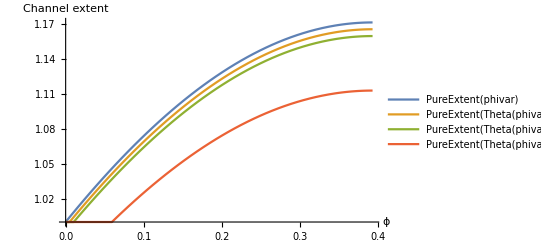

```mathematica
Plot[{PureExtent[phivar], PureExtent[Theta[phivar,0.005]],PureExtent[Theta[phivar,0.01]],PureExtent[Theta[phivar,0.05]]}, {phivar,0, Pi/8}, PlotLegends->"Expressions",AxesLabel->{ϕ,"Channel extent"}]
```

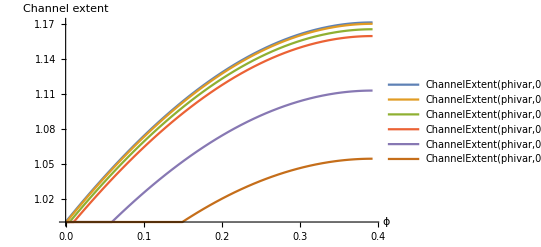

```mathematica
ChannelExtent[phi_,p_] := PureExtent[Theta[phi,p]]
Plot[{ChannelExtent[phivar,0],  ChannelExtent[phivar,0.001],ChannelExtent[phivar,0.005],ChannelExtent[phivar,0.01],ChannelExtent[phivar,0.05],ChannelExtent[phivar,0.1]}, {phivar,0, Pi/8}, PlotLegends->"Expressions",AxesLabel->{ϕ,"Channel extent"}]
```

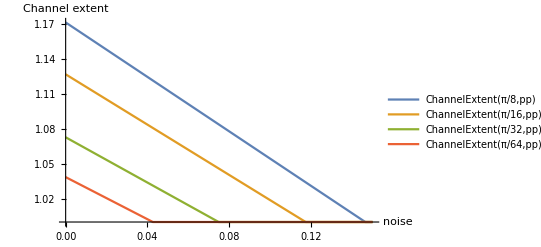

```mathematica
Plot[{ChannelExtent[Pi/8,pp],ChannelExtent[Pi/16,pp],ChannelExtent[Pi/32,pp],ChannelExtent[Pi/64,pp]},{pp,0,0.15},PlotLegends->"Expressions",AxesLabel->{"noise","Channel extent"}]
```

```mathematica
ManyCopyChannelExtent[N_,phi_,p_]:=ChannelExtent[phi,p]^N
```

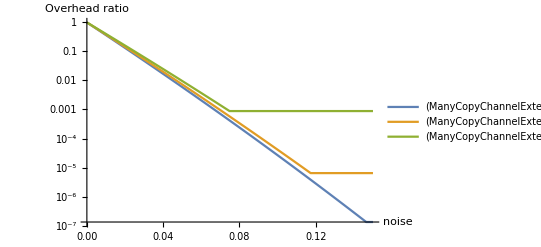

```mathematica
LogPlot[{ManyCopyChannelExtent[100,Pi/8,q]/ManyCopyChannelExtent[100,Pi/8,0],ManyCopyChannelExtent[100,Pi/16,q]/ManyCopyChannelExtent[100,Pi/16,0],ManyCopyChannelExtent[100,Pi/32,q]/ManyCopyChannelExtent[100,Pi/32,0]}, {q,0, 0.15},AxesLabel->{"noise","Overhead ratio"},PlotLegends->"Expressions"]
```